```mathematica
loadTable[path_]:= Import[NotebookDirectory[]<>path, "Table"]
totalColumn[raw_, colNum_]:= Total[Transpose[Drop[raw, 1]][[colNum]]]
allTotalColumns[rawList_, colNum_]:= Function[x, totalColumn[x, colNum]]/@ rawList
plotRunTimes[rawList_, varList_, predictorLabel_]:=(
searchTime = Transpose[{varList, allTotalColumns[rawList, 2]}];
veriTime = Transpose[{varList, allTotalColumns[rawList, 7]}];
totalRuntime = Transpose[{varList, allTotalColumns[rawList, 9]}];
referenceFunc = Transpose[{varList, Function[x, 600*x^2.4+500000000] /@varList}];
ListLinePlot[{searchTime, veriTime, totalRuntime, referenceFunc},  PlotRange->Full, Filling-> None, InterpolationOrder->1, PlotLegends->Placed[{"Search Step", "Verification Step", "Total", "REF"}, Above], AxesLabel->{predictorLabel, "runtime (ns)"}, ImageSize->Medium]
)
largestFilterBlockLength[raw_]:=Max[Transpose[Drop[raw, 1]][[1]]]
filterTime[raw_, blockLen_]:=(
pos = Position[Transpose[raw][[1]], blockLen];
If[pos=={} , 0,(raw[[pos[[1]]]])[[1]][[9]]]
)
filterTimeRatio[raw_, blockLen_]:=(
t = filterTime[raw, blockLen];
tot = totalColumn[raw, 9];
 t /tot
)
filterLine[rawList_, varList_, blockLen_]:= 
(
y = Function[x, filterTimeRatio[x, blockLen]] /@ rawList;
Transpose[{varList, y}]
)
plotFilterRatios[rawList_, varList_, predictorLabel_]:=
(
smallestFilter = 2;
largestFilter = Max[largestFilterBlockLength /@ rawList];
filterRange = Range[smallestFilter, largestFilter];
allLines =  Function[x, filterLine[rawList, varList, x]] /@ filterRange;
ListLinePlot[allLines,  PlotRange->Full, InterpolationOrder->1, PlotLegends->Placed[filterRange, Above], AxesLabel-> {predictorLabel, "proportion of\ntotal runtime"}, ImageSize->Medium]
)
bothPlots[pathsList_, varList_, predictorLabel_]:=
Module[{raws},
raws = loadTable/@ pathsList;
plotRunTimes[raws, varList,predictorLabel]
plotFilterRatios[raws, varList, predictorLabel]
]
runtimeCmpPlot[rawListList_, varList_, predictorLabel_, legends_]:=(
(*lines = Function[x, Transpose[{varList, allTotalColumns[x, 2]/allTotalColumns[x, 9]}]] /@ rawListList;*)
lines = Function[x, Transpose[{varList, allTotalColumns[x, 9]}]] /@ rawListList;
ListLogPlot[lines,  PlotRange->Full,Filling-> None, InterpolationOrder->1,Joined->True,  PlotLegends->Placed[legends, Right], AxesLabel->{predictorLabel, "search step\nruntime proportion"}, ImageSize->Medium]
)
```

```mathematica
raw = loadTable["/outputs/kucherov_2/5VM_real.p1.40000.out"];
TableForm[raw]
dropped = Drop[raw, 1];
trans = Transpose[dropped];
cols = trans[[2;;4]];
ready = Transpose[cols];


BarChart[ready, ChartLayout->"Stacked", ChartLabels->{Placed[trans[[1]],Axis],None}, PlotLabel->"Run times for filter-lengths\nfor coverage experiment {5VM_real.p1.40000}", ImageSize->Medium, ChartLegends->Placed[{"search", "verification: successes", "verification: failures"}, Below], AxesLabel->{"filter block\nlength", "runtime\ncontribution (ns)"}]

ListLinePlot[trans[[10]],Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotRange->{0,1}, PlotLabel->"Ratio of time spent searching", ImageSize->Medium, AxesLabel->{"filter block\nlength", "runtime\nproportion"}]
ListLinePlot[{trans[[5]], trans[[6]]},Filling->Axis, DataRange->{trans[[1]][[1]], trans[[1]][[-1]]}, PlotLabel->"Solution count", PlotLegends->Placed[{"Solutions", "Spurious Candidates"}, Below], ImageSize->Medium, AxesLabel->{"filter block\nlength", "solution\ncount"}]


plotRunTimes[]
```

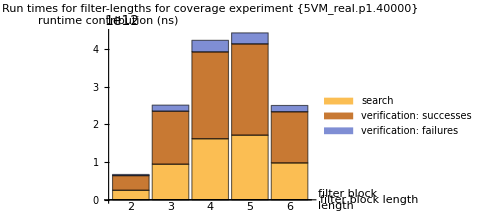
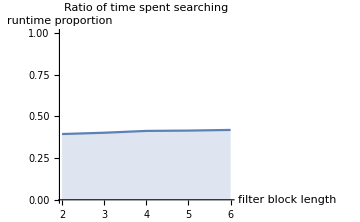
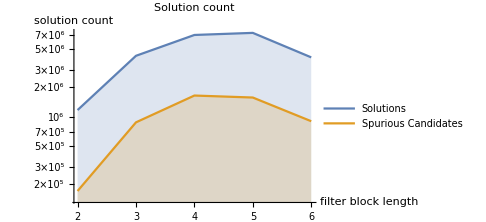

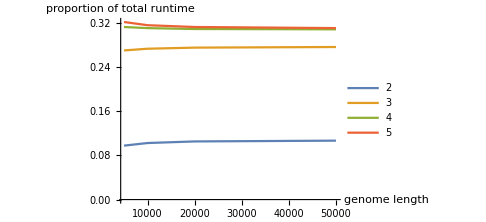
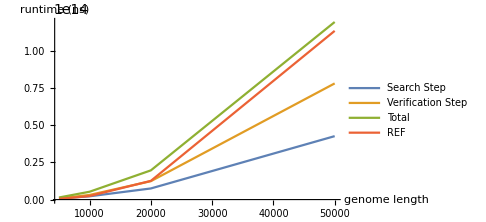

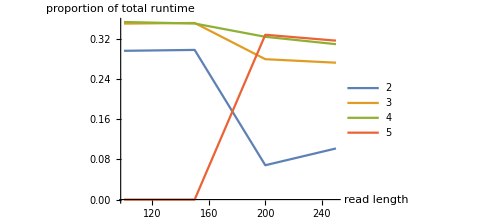
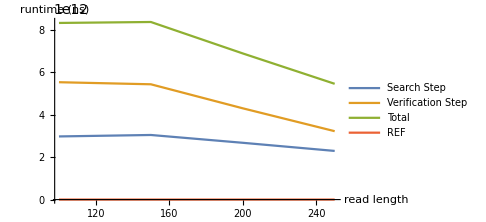

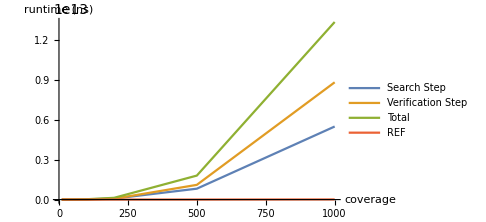

```mathematica
gnmlenVars = {5000, 10000, 20000, 50000};
gnmlenPaths = {
"/outputs/kucherov_2/reads.5000.out",
"/outputs/kucherov_2/reads.10000.out",
"/outputs/kucherov_2/reads.20000.out",
"/outputs/kucherov_2/reads.50000.out"
};
rdlenVars = {100, 150, 200, 250};
rdlenPaths = {
"/outputs/kucherov_2/hxb2.l100.reads.out",
"/outputs/kucherov_2/hxb2.l150.reads.out",
"/outputs/kucherov_2/hxb2.l200.reads.out",
"/outputs/kucherov_2/hxb2.l250.reads.out"
};
covVars = {10, 20, 50, 100, 200, 500, 1000};
covPaths = {
"/outputs/kucherov_2/5VM_real.p1.400.out",
"/outputs/kucherov_2/5VM_real.p1.800.out",
"/outputs/kucherov_2/5VM_real.p1.2000.out",
"/outputs/kucherov_2/5VM_real.p1.4000.out",
"/outputs/kucherov_2/5VM_real.p1.8000.out",
"/outputs/kucherov_2/5VM_real.p1.20000.out",
"/outputs/kucherov_2/5VM_real.p1.40000.out"
};
divVars = { 0.005, 0.01, 0.02, 0.04, 0.08};
divPaths = {
"/outputs/kucherov_2/mut0.005.out",
"/outputs/kucherov_2/mut0.01.out",
"/outputs/kucherov_2/mut0.02.out",
"/outputs/kucherov_2/mut0.04.out",
"/outputs/kucherov_2/mut0.08.out"
};

bothPlots[gnmlenPaths, gnmlenVars, "genome length"]
bothPlots[rdlenPaths, rdlenVars, "read length"]
bothPlots[covPaths, covVars, "coverage"]
bothPlots[divPaths, divVars, "divergence"]
```

```mathematica
cmpVars = {10, 20, 50, 100, 200};
pHam = {
"/partial_hamming/kucherov_2/5VM_real.p1.400.out",
"/partial_hamming/kucherov_2/5VM_real.p1.800.out",
"/partial_hamming/kucherov_2/5VM_real.p1.2000.out",
"/partial_hamming/kucherov_2/5VM_real.p1.4000.out",
"/partial_hamming/kucherov_2/5VM_real.p1.8000.out"
};
pathsA = {
"/outputs/kucherov_2/5VM_real.p1.400.out",
"/outputs/kucherov_2/5VM_real.p1.800.out",
"/outputs/kucherov_2/5VM_real.p1.2000.out",
"/outputs/kucherov_2/5VM_real.p1.4000.out",
"/outputs/kucherov_2/5VM_real.p1.8000.out"
};
pathsB = {
"/outputs/incls/5VM_real.p1.400.out",
"/outputs/incls/5VM_real.p1.800.out",
"/outputs/incls/5VM_real.p1.2000.out",
"/outputs/incls/5VM_real.p1.4000.out",
"/outputs/incls/5VM_real.p1.8000.out"
};
pathsC = {
"/outputs/edit/5VM_real.p1.400.out",
"/outputs/edit/5VM_real.p1.800.out",
"/outputs/edit/5VM_real.p1.2000.out",
"/outputs/edit/5VM_real.p1.4000.out",
"/outputs/edit/5VM_real.p1.8000.out"
};
pathsD = {
"/outputs/both/5VM_real.p1.400.out",
"/outputs/both/5VM_real.p1.800.out",
"/outputs/both/5VM_real.p1.2000.out",
"/outputs/both/5VM_real.p1.4000.out",
"/outputs/both/5VM_real.p1.8000.out"
};
rawListList = Function[x, loadTable/@ x] /@ {pathsA, pathsB, pathsC, pathsD};
runtimeCmpPlot[rawListList, cmpVars, "coverage", {"neither", "inclusions", "edit", "both"}]
```

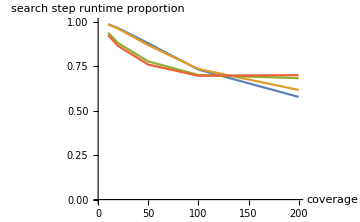

```mathematica
bl2 = {0,0,0};
bl3 = {0,0,1,1};
bl4 = {0,0,1,2,2};
bl5 = {0,0,1,2,3,3};
bl6 = {0,0,1,2,3,4,4};
ListLinePlot[{bl2, bl3, bl4, bl5, bl6}, AxesLabel->{"blocks matched", "pE"}, PlotLegends->Placed[ {"length=2", "length=3", "length=4", "length=5", "length=6"},Right]]
```

```mathematica
cmpVars = {10, 20, 50, 100, 200, 500};
pHam = {
"/outputs/partial_hamming/5VM_real.p1.400.out",
"/outputs/partial_hamming/5VM_real.p1.800.out",
"/outputs/partial_hamming/5VM_real.p1.2000.out",
"/outputs/partial_hamming/5VM_real.p1.4000.out",
"/outputs/partial_hamming/5VM_real.p1.8000.out",
"/outputs/partial_hamming/5VM_real.p1.20000.out"
};
ham = {
"/outputs/kucherov_2/5VM_real.p1.400.out",
"/outputs/kucherov_2/5VM_real.p1.800.out",
"/outputs/kucherov_2/5VM_real.p1.2000.out",
"/outputs/kucherov_2/5VM_real.p1.4000.out",
"/outputs/kucherov_2/5VM_real.p1.8000.out",
"/outputs/kucherov_2/5VM_real.p1.20000.out"
};
rawListList = Function[x, loadTable/@ x] /@ {ham, pHam};
runtimeCmpPlot[rawListList, cmpVars, "coverage", {"neither", "inclusions", "edit", "both"}]
```

```mathematica
manyLoad[prefix_, affixList_, suffix_]:=
(
paths = Function[x, prefix<>ToString[x]<>suffix]/@affixList;
loadTable/@ paths
)
manyManyLoad[pathPrefix_, folderList_, filePrefix_, fileAffixList_, fileSuffix_]:=
(
x = Function[x, manyLoad[pathPrefix<>x<>filePrefix, fileAffixList, fileSuffix]]/@folderList;
x
)
folders = {"valimaki2","kucherov_1","kucherov_2", "kucherov_3", "kucherov_4", "kucherov_5", "kucherov_6"}
coverages = {400, 800, 2000, 4000, 8000, 20000};
realCoverages = {10, 20, 50, 100, 200, 500};

mm = manyManyLoad["/outputs/", folders, "/5VM_real.p1.", coverages, ".out"];
runtimeCmpPlot[mm, realCoverages, "coverage", folders]
largestFilter = Max[largestFilterBlockLength /@ Flatten[mm, 1]];
raw2col[raw_]:=filterTime[raw, #]& /@Range[1, largestFilter]
c400s =(#[[1]])&/@mm;
c20000s =(#[[6]])&/@mm;
cl = {Placed[folders,Axis, Rotate[#,-Pi/2]&],None};
BarChart[raw2col/@c400s, ChartLayout->"Stacked",ChartLegends->{Range[1,largestFilter]},  ChartLabels->cl, ImageSize->Large, AxesLabel->{"Algorithm", "runtime (ns)"},ChartStyle->"Rainbow"]

BarChart[raw2col/@c20000s, ChartLayout->"Stacked",ChartLegends->{Range[1,largestFilter]},  ChartLabels->cl, ImageSize->Large, AxesLabel->{"Algorithm", "runtime (ns)"}]
```

```mathematica
x = 400000
x / 150 * 30
```

400000

80000